## Первое приближение

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3 10^8; (* м/c *)
Γ = 6 10^6 /10^6(* МГц *);
vQ = 1200; (* м/c *)
s = 100;
```

```mathematica
ClearAll[f01, f02, F];
f01[ν0_, ν_, v_] := (1-s/(1 +s+ 4 (ν - ν0(1+ v/c))^2/Γ^2))1/(1  + 4 (ν - ν0(1- v/c))^2/Γ^2);
F1[ν_] :=  NIntegrate[
(f01[ν0, ν, v] +f01[ν0 + 9, ν, v]+f01[ν0 + 15, ν, v])Exp[- v^2/vQ^2]
, {v, -2 vQ, + 2 vQ}, MaxRecursion->12];
F2[ν_] :=  NIntegrate[
(f01[ν0, ν, v] +f01[ν0 + 6, ν, v]+f01[ν0 + 9, ν, v])Exp[- v^2/vQ^2]
, {v, -2 vQ, + 2 vQ}, MaxRecursion->12];
```

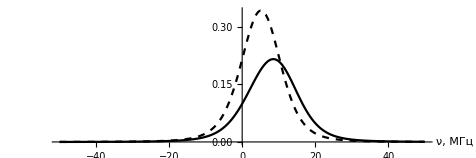

```mathematica
border = 50;
DiscretePlot[
{Exp[-F1[ν0+ν](-Log[0.1]/F1[ν0] )], Exp[-F2[ν0+ν](-Log[0.1]/F1[ν0] )]}, {ν,-border, + border, border / 100}, Filling->None, Joined->True, AxesLabel->{"ν, МГц",}, AspectRatio->1/3, PlotRange->All, PlotStyle->{{Black}, {Black, Dashed}}]
```

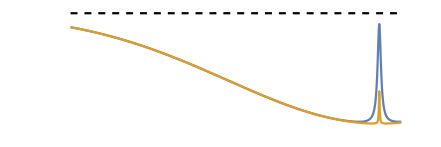

```mathematica
ϵ =8 10^-6;
image2 = DiscretePlot[
{-f1[100, ν0+ν], -f1[1, ν0+ν],0}, {ν,- 0.7ϵ ν0, +ϵ ν0/20, ϵ ν0 / 1000}, PlotRange->Full,Filling->None, Joined->True, PlotStyle->{,,{Dashed, Black}},AxesLabel->{"ν, МГц", "~ Log[I_out/I_in]"}, Axes->False, AspectRatio->1/3]
```

```mathematica
(*Export[NotebookDirectory[]<>"v2.png", image2]*)
```

## Оценка κ

```mathematica
kB= 1.38 10^-23;
ℏ = 1 10^-34;
Na = 6.02 10^23;
R = Na kB;
m = 0.007 / Na;
M = 0.007;
T = 300 + 273;
vQ = √((2 kB T)/m);
Print["<v> = ", ScientificForm[vQ, 2], " м/c"]
```

<v> = 1.2×10^3 м/c

```mathematica
ClearAll[GetP];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);
n = GetP[T]/(kB T);
Print["концентрация n = ", ScientificForm[n, 2], " (:043c)^-3"]
```

концентрация n = 1.2×10^16 м^-3

```mathematica
l = 0.1; (* м, -- область пересечения лучей *)
σ0 = 4 π(10^-9)^2;
κ = σ0 n l √(m/(2 π kB T));
Print["κ = ", ScientificForm[κ, 2], " (м/c)^-1"]
```

κ = 7.3×10^-6 (м/c)^-1

```mathematica
σ0 n l
```

0.0150541

## Оценка контрастности

Оценим параметр κ из отношения β = I_out / I_in в глубине доплеровского провала.

```mathematica
β = 1/6; (* β = Subscript[I, out] / Subscript[I, in] *)
κx = -Log[β]/f1[0, ν0] (* c/м *)
```

0.284285

```mathematica
ClearAll[GetK];
GetK[β_, s_] :=  (β^(f1[s, ν0]/f1[0, ν0])-β)/(1-β);
```

```mathematica
im3 = DiscretePlot[{100GetK[0.9, s], 100GetK[0.5, s], 100GetK[0.1, s]}, {s, 0, 3, 0.01}, Joined->True, Filling->None, (*PlotLabel->"Зависимость контрастности от параметра насыщения", *)(*PlotStyle->{RGBColor[0.,0.57,0.], Thickness[10^-2]}, *)GridLines->Automatic, AxesLabel->{MaTeX["s"], MaTeX["K,\\, \\%"]}, ImageSize->{300,150}, PlotLabels->{MaTeX["\\beta = 0.9"], MaTeX["\\beta = 0.5"], MaTeX["\\beta = 0.1"]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"K.png", im3]
```

D:\Kami\git_folder\notes_5sem\rqc\saturation_spectr_simulation\K.png

```mathematica
<<MaTeX`
```

-Graphics-